```mathematica
(*Avtomatsko shranjevanje notebook-a*)
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

# Vaje za 3. teden

5.  3.  2026

## Naloga 1

V pomoči si poglej ukaz Join. Definiraj seznam {1,2,...,100,1,2,...,100}. Definiraj še funkcijo DvojniSeznam[n], ki vrne dvojni seznam {1,2,...,n,1,2,...,n}.

```mathematica
seznam=Join[Range[100],Range[100]]
DvojniSeznam[m_] := Join[Range[m],Range[m]]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

Kaj dela spodnja funkcija?

```mathematica
Krogi[n_]:=Join[{Red},Table[Disk[{2i,0}],{i,n}]]
```

Definiraj funkcijo NarisiKroge[n], ki nariše n rdečih krogov. Barve lahko definiraš tudi drugače, uporabi domišljijo. Pomagaj si s funkcijo Graphics. Na primer, klic NarisiKroge[5] naj vrne nekaj takega kot:

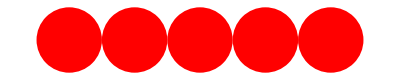

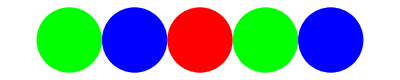

-Graphics3D-

```mathematica
NarisiKroge[n_]:=Graphics[{Red,Table[Disk[{2 i,0},1],{i,n}]}]
NarisiKroge[5]
ClearAll[n]
MesaniKroge[n_]:=Module[{colors={Green,Blue,Red}},Graphics[Table[{colors[[Mod[i-1,Length[colors]]+1]],Disk[{2 i,0},1]},{i,n}]]]
MesaniKroge[5]
ClearAll[n]
NarisiKrogle[n_]:=Graphics3D[{Specularity[White,20],Orange,Table[Sphere[{2 i,i,0},1],{i,n}]}]
NarisiKrogle[3]
Manipulate[Graphics3D[{Sphere[{2,y1,0},1],Sphere[{4,y2,0},1],Sphere[{6,y3,0},1]},PlotRange->{{0,8},{-5,5},{-2,2}}],{y1,-3,3},{y2,-3,3},{y3,-3,3}]
```

Za dodatni izziv poskusi napisati funkcijo MesaniKrogi[n], ki bo narisala kroge v izmenjajočih barvah. Na primer:
-Graphics-

Na podoben način definiraj še funkcijo NarisiKrogle[n], ki nariše n sfer. Sfere lahko postaviš tudi drugače (ne nujno v ravni vrsti).

Nariši interaktivni 3d graf, ki vsebuje tri zaporedne krogle, vsaki od katerih lahko spreminjaš njeno drugo koordinato.

-Graphics3D-

## Naloga 2

Napiši funkcijo, ki sprejme narvni števili m in n in vrne seznam prvih n členov Collatzovega zaporedja za število m. Pomagaj si s funkcijo “RecurrenceTable”.

```mathematica
ClearAll[n]
Collatz[m_,n_]:=RecurrenceTable[{a[i+1]==If[EvenQ[a[i]],a[i]/2,3 a[i]+1],a[1]==m},a,{i,n}]
Collatz[10, 5]
```

{10,31,94,283,850}

## Naloga 3

Napiši  funkcijo quickSort, ki sprejme seznam in vrne urejen seznam. Za urejanje naj uporabi algoritem Quick sort.

```mathematica
quickSort[{}]:={}
quickSort[{pivot_,rest___}]:=Join[quickSort[Select[{rest},#<pivot&]],{pivot},quickSort[Select[{rest},#>=pivot&]]]
```

## Naloga 4

Napiši funkcijo odvod polinoma, ki kot argument sprejme polinom v splošni obliki in vrne njegov odvod. Pri tem uporabi le prepisovalna pravila.

```mathematica
odvodPolinoma[polinom_]:=polinom/. {x_^n_.:>n*x^(n-1),c_*x_:>c,c_?NumericQ:>0}
odvodPolinoma[x^3 + x^2+5x]
```

1